```mathematica
BigTab=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\BIGTAB1300.DAT","Table"];
BigTab=Drop[BigTab,200];
BigTab=Drop[BigTab,0];
```

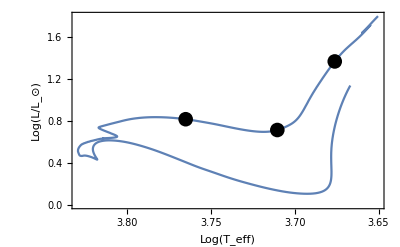

```mathematica
LogTLogL=BigTab[[All,{5,4}]];
Show[ListPlot[LogTLogL,ScalingFunctions->{"Reverse",Identity},Frame->True,Joined->True,FrameLabel->{"Log(T_eff)","
Log(L/L_⊙)"},LabelStyle->Black,BaseStyle->{FontWeight->"Plain",FontSize->10}],ListPlot[{BigTab[[1330,{5,4}]],BigTab[[1370,{5,4}]],BigTab[[1530,{5,4}]]},PlotMarkers->{"●",15},PlotStyle->Black,ScalingFunctions->{"Reverse",Identity},Frame->True]]
```

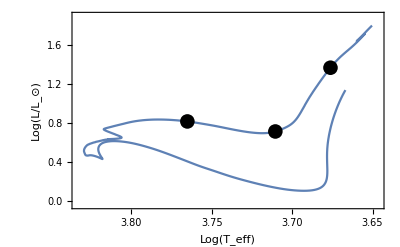

-Graphics-

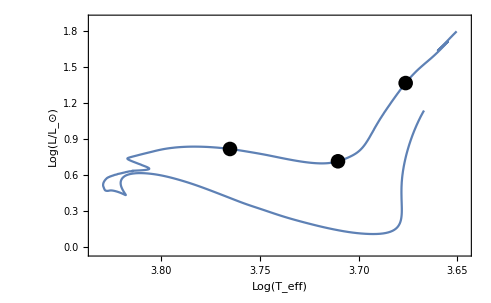
```mathematica
HRDiagram=-Graphics-;
```

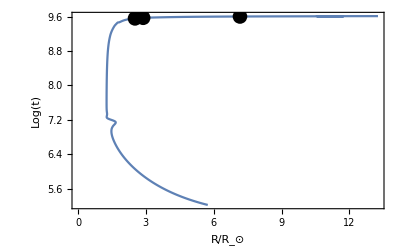

```mathematica
RLogAge=BigTab[[All,{20,2}]];
RLogAgePlot=Show[ListPlot[RLogAge,Frame->True,Joined->True,FrameLabel->{"R/R_⊙","
Log(t)"},BaseStyle->{FontWeight->"Plain",FontSize->14},LabelStyle->Black],ListPlot[{BigTab[[1330,{20,2}]],BigTab[[1370,{20,2}]],BigTab[[1530,{20,2}]]},PlotMarkers->{"●",15},PlotStyle->Black,Frame->True]]
```

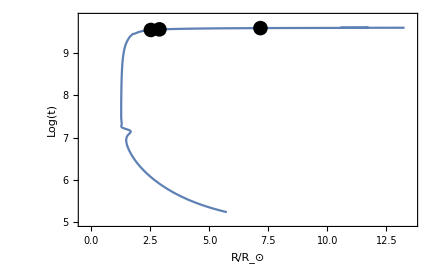

-Graphics-

```mathematica
RLogAgePlot=-Graphics-;
```

```mathematica
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\pic1_HRDiagram.png",HRDiagram,ImageResolution->150]
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\pic2_RadiusPlot.png",RLogAgePlot,ImageResolution->150]*)
```

C:\Users\Pigkappa\Dropbox\fisica\PhD\AngularMomentumTransfer\VariousModels\pic1_HRDiagram.png

```mathematica
Graphics[Inset["RG_1"]];
Graphics[Inset["RG_2"]];
Graphics[Inset["RG_3"]];
```